# Word Cloud Images

```mathematica
data=EntityValue[CountryData[],{"Name","Population"}];
```

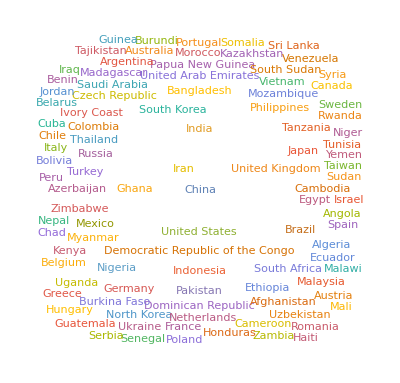

```mathematica
WordCloud[data]
```

```mathematica
WordCloud[data,ImageSize->Full]
```

-Graphics-

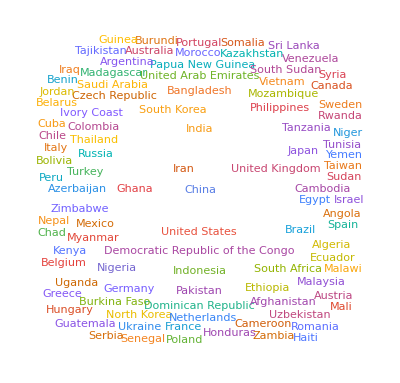

```mathematica
WordCloud[data,ImageSize->Full,PlotTheme->"Business"]
```

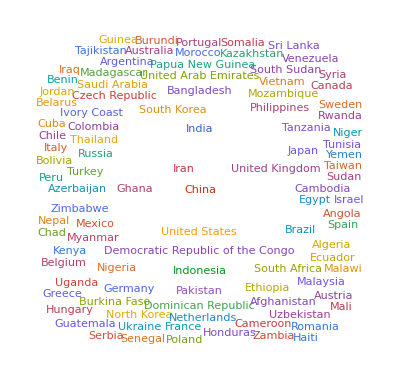

```mathematica
WordCloud[data,ImageSize->Full,PlotTheme->"Web"]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"word cloud of countries weighted by population data with business plot theme.svg"}],WordCloud[data,ImageSize->Full,PlotTheme->"Business"]]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\word cloud of countries weighted by population data with business plot theme.svg

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"word cloud of countries weighted by population data with web plot theme.svg"}],WordCloud[data,ImageSize->Full,PlotTheme->"Web"]]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\word cloud of countries weighted by population data with web plot theme.svg